```mathematica
(* ===1. Новая структура компоненты с функциями===*)spec=<|MaxTime->10,SampleRate->1000,Components->{<|AFunc->Function[t,2+0.5*Sin[2 Pi*0.2 t]],FFunc->Function[t,5+5*t/10],TStart->0,TEnd->10|>,(*частота от 5 до 10 Гц*)<|AFunc->Function[t,1],FFunc->Function[t,7.5+2.5*Sin[2 Pi*0.5*t]],TStart->2,TEnd->6|>,(*частота "дышит" 5–10 Гц*)<|AFunc->Function[t,1+0.5*Sin[2 Pi*0.1*t]],FFunc->Function[t,9],TStart->4,TEnd->8|>    (*частота постоянная,амплитуда "дышит"*)}|>;
```

```mathematica
tValues=Range[0,spec[MaxTime],1/spec[SampleRate]];

data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],#[AFunc][t]*Sin[2 Pi*#[FFunc][t]*t],0]&,spec[Components]]},{t,tValues}];
```

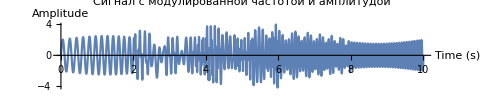

```mathematica
ListLinePlot[data,PlotLabel->"Сигнал с модулированной частотой и амплитудой",AxesLabel->{"Time (s)","Amplitude"},ImageSize->1000,AspectRatio->1/5]
```

```mathematica
WindowSpectrogram[data_,sampleRate_,windowSize_,stepSize_]:=Module[{n=Length[data],windows,result,freqs,timeCenters},windows=Table[Take[data,{i,i+windowSize-1}],{i,1,n-windowSize+1,stepSize}];
result=FourierMagnitude/@windows;
freqs=Range[0,Floor[windowSize/2]-1]*sampleRate/windowSize;
result=result[[All, ;;Floor[windowSize/2]]];
timeCenters=Range[1,Length[windows]]*stepSize/sampleRate;
{freqs,timeCenters,Transpose[result]}];

FourierMagnitude[v_]:=2*Abs[Fourier[v,FourierParameters->{1,-1}]]/Length[v];
```

```mathematica
{freqs,times,spectro}=WindowSpectrogram[data[[All,2]],spec[SampleRate],256,32];

ListPlot3D[spectro,DataRange->{{times[[1]],times[[-1]]},{freqs[[1]],freqs[[-1]]}},AxesLabel->{"Time (s)","Frequency (Hz)","Amplitude"},ColorFunction->"SunsetColors",Mesh->None,PlotLabel->"3D спектрограмма сигнала с модулированной частотой/амплитудой"]
```

-Graphics3D-